#### Dimensionful 2D dynamical model for feedback

```mathematica
A1= {{ 0,λ},{-κ2, κ1}}
B1 = {{σx,0},{0,κ2*σy }}
Eigenvalues[A1]
Eigenvectors[A1]
s=Array[X,{2,2}]
s/. Expand[Solve[A1.s+s.Transpose[A1]==B1.Transpose[B1], Flatten[s]]]
```

{{0,λ},{-κ2,κ1}}

{{σx,0},{0,κ2 σy}}

{1/2 (κ1-√(κ1^2-4 κ2 λ)),1/2 (κ1+√(κ1^2-4 κ2 λ))}

{{-(-κ1-√(κ1^2-4 κ2 λ))/(2 κ2),1},{-(-κ1+√(κ1^2-4 κ2 λ))/(2 κ2),1}}

{{X[1,1],X[1,2]},{X[2,1],X[2,2]}}

{{{σx^2/(2 κ1)+(κ1 σx^2)/(2 κ2 λ)+(κ2 λ σy^2)/(2 κ1),σx^2/(2 λ)},{σx^2/(2 λ),(κ2 σx^2)/(2 κ1 λ)+(κ2^2 σy^2)/(2 κ1)}}}

#### Dimensionless feedback

```mathematica
A3= {{ 0,λt},{-κt, κt}}
B3 = {{1,0},{0,κt }}
Eigenvalues[A3]
eigens = FullSimplify[Eigenvectors[A3]]
s3=Array[Y,{2,2}]
s3/. Expand[FullSimplify[Solve[A3.s3+s3.Transpose[A3]==B3.Transpose[B3], Flatten[s3]]]]
```

{{0,λt},{-κt,κt}}

{{1,0},{0,κt}}

{1/2 (κt-√κt √(κt-4 λt)),1/2 (κt+√κt √(κt-4 λt))}

{{1/2 (1+(√(κt-4 λt))/(√κt)),1},{1/2-(√(κt-4 λt))/(2 √κt),1}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{{1/(2 κt)+1/(2 λt)+λt/2,1/(2 λt)},{1/(2 λt),κt/2+1/(2 λt)}}}

```mathematica
FullSimplify[(MatrixExp[-A3*t].{x0, y0})]
```

{ⅇ^(-(t κt)/2) (x0 Cosh[1/2 t √κt √(κt-4 λt)]+((x0 κt-2 y0 λt) Sinh[1/2 t √κt √(κt-4 λt)])/(√κt √(κt-4 λt))),ⅇ^(-(t κt)/2) (y0 Cosh[1/2 t √κt √(κt-4 λt)]+((2 x0-y0) √κt Sinh[1/2 t √κt √(κt-4 λt)])/(√(κt-4 λt)))}

```mathematica
Manipulate[Show[{ParametricPlot[%12, {t, 0, 100}, PlotRange->10], Plot[{(1/2 (1+(√(κt-4 λt))/(√κt)))^-1 x,(1/2 (1-(√(κt-4 λt))/(√κt)))^-1 x}, {x, 0, 10}, PlotStyle->Dashed]}], {λt, 0.05, 0.2}, {κt, 5, 10}, {x0, 1, 8}, {y0, 1, 8}]
```

#### Dimensionless, unamplified noise model

```mathematica
A= {{ 0,λt},{-1, 1}}
```

{{0,λt},{-1,1}}

```mathematica
X0={x0, y0}
```

{x0,y0}

```mathematica
Eigenvectors[A]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

```mathematica
MatrixExp[-A*t].X0
```

{x0 (-(ⅇ^(1/2 t (-1-√(1-4 λt))) (1-√(1-4 λt)))/(2 √(1-4 λt))+(ⅇ^(1/2 t (-1+√(1-4 λt))) (1+√(1-4 λt)))/(2 √(1-4 λt)))+y0 ((ⅇ^(1/2 t (-1-√(1-4 λt))) λt)/(√(1-4 λt))-(ⅇ^(1/2 t (-1+√(1-4 λt))) λt)/(√(1-4 λt))),x0 (-ⅇ^(1/2 t (-1-√(1-4 λt)))/(√(1-4 λt))+ⅇ^(1/2 t (-1+√(1-4 λt)))/(√(1-4 λt)))+y0 (-(ⅇ^(1/2 t (-1-√(1-4 λt))) (-1-√(1-4 λt)))/(2 √(1-4 λt))+(ⅇ^(1/2 t (-1+√(1-4 λt))) (-1+√(1-4 λt)))/(2 √(1-4 λt)))}

```mathematica
X[t_, x0_, y0_, λt_] = FullSimplify[%]
```

{ⅇ^(-t/2) (x0 Cosh[1/2 t √(1-4 λt)]+((x0-2 y0 λt) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt))),ⅇ^(-t/2) (y0 Cosh[1/2 t √(1-4 λt)]+((2 x0-y0) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt)))}

#### Solve for the time y(t*)=1 and evaluate x(t*).

```mathematica
λt0 = 0.04;
c=2/(1+Sqrt[1-4λt0]);
cf = 2/(1+Sqrt[1-4λ])
x0h = 2;
y0h =x0h*c
```

2/(1+√(1-4 λ))

2.08712

```mathematica
x0Range = Table[p, {p, x0h-0.5, x0h+0.5, 0.01}];
y0Range = Table[p, {p,y0h-0.5, y0h+0.5, 0.01}];
```

```mathematica
params = Flatten[Table[{x0->x, y0->y, λt->λt0}, {x, x0Range}, {y, y0Range}], 1]
```

{{x0→1.5,y0→1.58712,λt→0.04},{x0→1.5,y0→1.59712,λt→0.04},{x0→1.5,y0→1.60712,λt→0.04},{x0→1.5,y0→1.61712,λt→0.04},{x0→1.5,y0→1.62712,λt→0.04},{x0→1.5,y0→1.63712,λt→0.04},10189,{x0→2.5,y0→2.53712,λt→0.04},{x0→2.5,y0→2.54712,λt→0.04},{x0→2.5,y0→2.55712,λt→0.04},{x0→2.5,y0→2.56712,λt→0.04},{x0→2.5,y0→2.57712,λt→0.04},{x0→2.5,y0→2.58712,λt→0.04}}
 |  |  |  |

```mathematica
tSolver [params_]:=FindRoot[(ⅇ^(-t/2) (y0 Cosh[1/2 t √(1-4 λt)]+((2 x0-y0) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt)))==1)/.params, {t,(1/λt)/.params}, AccuracyGoal->16][[1]]
```

```mathematica
tvals = MapThread[tSolver, {params}]
```

{t→10.7198,t→10.7128,t→10.7059,t→10.6989,t→10.6919,t→10.6849,t→10.678,t→10.671,t→10.664,t→10.657,t→10.65,10179,t→23.0234,t→23.0192,t→23.0151,t→23.0109,t→23.0067,t→23.0025,t→22.9984,t→22.9942,t→22.99,t→22.9858,t→22.9816}
 |  |  |  |

```mathematica
results = Transpose[{params, tvals}]
res = Table[AppendTo[r[[1]], r[[2]]], {r, results}]
```

{{{x0→1.5,y0→1.58712,λt→0.04},t→10.7198},{{x0→1.5,y0→1.59712,λt→0.04},t→10.7128},{{x0→1.5,y0→1.60712,λt→0.04},t→10.7059},{{x0→1.5,y0→1.61712,λt→0.04},t→10.6989},10194,{{x0→2.5,y0→2.56712,λt→0.04},t→22.99},{{x0→2.5,y0→2.57712,λt→0.04},t→22.9858},{{x0→2.5,y0→2.58712,λt→0.04},t→22.9816}}
 |  |  |  |

{{x0→1.5,y0→1.58712,λt→0.04,t→10.7198},{x0→1.5,y0→1.59712,λt→0.04,t→10.7128},{x0→1.5,y0→1.60712,λt→0.04,t→10.7059},{x0→1.5,y0→1.61712,λt→0.04,t→10.6989},10194,{x0→2.5,y0→2.56712,λt→0.04,t→22.99},{x0→2.5,y0→2.57712,λt→0.04,t→22.9858},{x0→2.5,y0→2.58712,λt→0.04,t→22.9816}}
 |  |  |  |

```mathematica
xpoints =Table[ⅇ^(-t/2) (x0 Cosh[1/2 t √(1-4 λt)]+((x0-2 y0 λt) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt)))/.p, {p, res}];
```

```mathematica
grid = Flatten[Table[{x,y}, {x, x0Range}, {y, y0Range}], 1]
```

{{1.5,1.58712},{1.5,1.59712},{1.5,1.60712},{1.5,1.61712},{1.5,1.62712},{1.5,1.63712},{1.5,1.64712},{1.5,1.65712},{1.5,1.66712},{1.5,1.67712},10181,{2.5,2.49712},{2.5,2.50712},{2.5,2.51712},{2.5,2.52712},{2.5,2.53712},{2.5,2.54712},{2.5,2.55712},{2.5,2.56712},{2.5,2.57712},{2.5,2.58712}}
 |  |  |  |

```mathematica
Transpose[{grid, xpoints}]
```

{{{1.5,1.58712},0.958257},{{1.5,1.59712},0.958257},{{1.5,1.60712},0.958256},{{1.5,1.61712},0.958256},{{1.5,1.62712},0.958255},10191,{{2.5,2.54712},0.958258},{{2.5,2.55712},0.958258},{{2.5,2.56712},0.958258},{{2.5,2.57712},0.958258},{{2.5,2.58712},0.958258}}
 |  |  |  |

```mathematica
f = Interpolation[Transpose[{grid, xpoints}]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[f[x, y], {x,x0h-0.5, x0h+0.5}, {y, y0h-0.5, y0h+0.5}, AxesLabel->{"x", "y"}]
```

-Graphics3D-

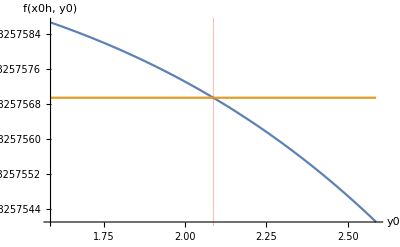

```mathematica
Show[{Plot[{f[x0h, y], 1/c},  {y, y0h-0.5, y0h+0.5}, AxesLabel->{"y0", "f(x0h, y0)"}, GridLines-> {{{y0h,Red}},None}]}]
```

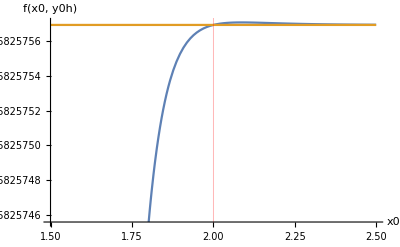

```mathematica
Plot[{f[x, y0h],1/c},  {x, x0h-0.5, x0h+0.5}, AxesLabel->{"x0", "f(x0, y0h)"}, GridLines-> {{{x0h,Red}},None}]
```

```mathematica
hess = ({{D[f[x, y], {x,2}],D[f[x, y], x,y]},{D[f[x, y], x,y],D[f[x, y], {y,2}]}})/.{x->x0h, y->y0h}
```

{{-1.11107×10^-6,5.53922×10^-7},{5.53922×10^-7,-4.43034×10^-8}}

```mathematica
D[f[x, y], {y}]/.{x->x0h, y->y0h}
```

-4.42388×10^-8

```mathematica
D[f[x, y], {x}]/.{x->x0h, y->y0h}
```

4.61335×10^-8

```mathematica
f[x, y]/.{x->x0h, y->y0h}
```

0.958258

```mathematica
VarFunc[fp_, s_]:=s^2 fp^2;
MeanFunc[f_, f2p_, s_]:=f+s^2 f2p/2;
```

#### width and mean with sx, lambda

```mathematica
VarFunc[%179,  sx](*Lambda=0.04*)
MeanFunc[%180, %177[[2,2]], sx]
```

2.1283×10^-15 sx^2

0.958258-2.21517×10^-8 sx^2

```mathematica
VarFunc[%150,  sx](*Lambda=0.08*)
MeanFunc[%151, %148[[2,2]], sx]
```

8.06906×10^-8 sx^2

0.912311-0.000129949 sx^2

#### width and mean with sx, lambda

```mathematica
VarFunc[-1.4192503154190848*^-6,  sy](*Lambda=0.05*)
MeanFunc[0.9472135954999574, -1.4235868039947535*^-6, sy]
```

2.01427×10^-12 sy^2

0.947214-7.11793×10^-7 sy^2

```mathematica
VarFunc[0.00028406099397508246,  sx](*Lambda=0.08*)
MeanFunc[0.9123105625617658, -0.0032701940821938495, sx]
```

8.06906×10^-8 sx^2

0.912311-0.0016351 sx^2

```mathematica
Manipulate[Show[{ParametricPlot[X[t, x0, y0, λt], {t, 0, 100}, PlotRange->2], Plot[{(1/2 (1+√(1-4 λt)))^-1 x,(1/2 (1-√(1-4 λt)))^-1 x, 1}, {x, 0, 2}, PlotStyle->Dashed]}], {λt, 0.02, 0.24}, {x0, 1, 10}, {y0, 1, 10}]
```

```mathematica
Σ[t]=FullSimplify[MatrixExp[-A*t].{{sx0, sxy0},{sxy0, sy0}}.MatrixExp[-Transpose[A]*t]]
```

{{1/(-1+4 λt)(-Cosh[t]+Sinh[t]) (-2 λt (sx0-sxy0+sy0 λt)+(sx0-2 (sx0+sxy0) λt+2 sy0 λt^2) Cosh[t √(1-4 λt)]+√(1-4 λt) (sx0-2 sxy0 λt) Sinh[t √(1-4 λt)]),1/(-1+4 λt)ⅇ^-t (sx0-sxy0+sy0 λt-(sx0+(-4 sxy0+sy0) λt) Cosh[t √(1-4 λt)]+√(1-4 λt) (-sx0+sy0 λt) Sinh[t √(1-4 λt)])},{1/(-1+4 λt)ⅇ^-t (sx0-sxy0+sy0 λt-(sx0+(-4 sxy0+sy0) λt) Cosh[t √(1-4 λt)]+√(1-4 λt) (-sx0+sy0 λt) Sinh[t √(1-4 λt)]),1/(2 (-1+4 λt))ⅇ^(-t (1+√(1-4 λt))) (-2 (-1+ⅇ^(t √(1-4 λt)))^2 sx0+2 ⅇ^(t √(1-4 λt)) (-2 sxy0+2 sy0 λt+(2 sxy0+sy0 (-1+2 λt)) Cosh[t √(1-4 λt)]+(-2 sxy0+sy0) √(1-4 λt) Sinh[t √(1-4 λt)]))}}

```mathematica
VarDiff = FullSimplify[Σ[t][[1,1]]+Σ[t][[2,2]]-Σ[t][[1,2]]]
```

1/(-1+4 λt)ⅇ^-t ((1+2 λt) (sx0-sxy0+sy0 λt)+(-1+λt) ((2 sx0-2 sxy0+sy0-2 sy0 λt) Cosh[t √(1-4 λt)]+(2 sxy0-sy0) √(1-4 λt) Sinh[t √(1-4 λt)]))

```mathematica
%/.t->(2 Log[1/x0])/(-1+√(1-4 λt))
```

1/(-1+4 λt)(1/x0)^(-2/(-1+√(1-4 λt))) ((1+2 λt) (sx0-sxy0+sy0 λt)+(-1+λt) ((2 sx0-2 sxy0+sy0-2 sy0 λt) Cosh[(2 √(1-4 λt) Log[1/x0])/(-1+√(1-4 λt))]+(2 sxy0-sy0) √(1-4 λt) Sinh[(2 √(1-4 λt) Log[1/x0])/(-1+√(1-4 λt))]))

```mathematica
Manipulate[Plot[%, {λt, 0.02, 0.26}, PlotRange->{0, 0.1}], {x0, 5, 8}, {sx0, 0.1, 3}, {sy0,0.1, 3}, {sxy0, 0, 3}]
```

#### Implicit differentiation for f(x0, y0)

```mathematica
DSolve[{y'[x]==1/λ-x/(λ *y[x])}, y[x], x, Assumptions->{1-4λ>0, λ>0}]
```

Solve[-ArcTanh[(-1+(2 λ y[x])/x)/(√(1-4 λ))]/(√(1-4 λ) λ)+Log[1-y[x]/x+(λ y[x]^2)/x^2]/(2 λ)==C[1]-Log[x]/λ,y[x]]

```mathematica
FullSimplify[%1, Assumptions->{x>0, y[x]>0, 1-4λ>0, λ>0}]
```

Solve[2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) (-2 λ C[1]+Log[x^2-x y[x]+λ y[x]^2])==0,y[x]]

```mathematica
Solve[2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) (-2 λ C[1]+Log[x^2-x y[x]+λ y[x]^2])==0, C[1]]
```

{{C[1]→(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) Log[x^2-x y[x]+λ y[x]^2])/(2 √(1-4 λ) λ)}}

```mathematica
g[δ]=TrigToExp[FullSimplify[2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->1, x-> 1/cf + δ},  Assumptions->{1-4λ>0,λ>0}]]
```

√(1-4 λ) Log[δ (δ+√(1-4 λ))]-Log[1-(1+2 δ+√(1-4 λ)-4 λ)/((1+2 δ+√(1-4 λ)) √(1-4 λ))]+Log[1+(1+2 δ+√(1-4 λ)-4 λ)/((1+2 δ+√(1-4 λ)) √(1-4 λ))]

```mathematica
Series[g[δ], {δ, 0, 1}, Assumptions->δ∈Reals]
```

(√(1-4 λ) Log[δ √(1-4 λ)]+Log[(2 (1+√(1-4 λ)-4 λ))/((1+√(1-4 λ)) √(1-4 λ))]-Log[-(8 δ λ)/((1+√(1-4 λ))^2 √(1-4 λ))])-(4 (-1-√(1-4 λ)+3 λ+√(1-4 λ) λ) δ)/((1+√(1-4 λ)) (1+√(1-4 λ)-4 λ))+O[δ]^2

```mathematica
h[x0,ϵ0]=FullSimplify[2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->(cf*x0)+ϵ0, x->x0},Assumptions->{1-4λ>0, x0>0, λ>0}]
```

2 ArcTanh[1-(2 ϵ0 λ)/(x0 √(1-4 λ))]+√(1-4 λ) Log[ϵ0 (-x0 √(1-4 λ)+ϵ0 λ)]

```mathematica
Series[h[x0, ϵ0], {ϵ0, 0, 1}, Assumptions->ϵ0∈Reals]
```

(Log[2]+√(1-4 λ) Log[-x0 ϵ0 √(1-4 λ)]-Log[(2 ϵ0 λ)/(x0 √(1-4 λ))])-((1+√(1-4 λ)) λ ϵ0)/(x0 √(1-4 λ))+O[ϵ0]^2

```mathematica
FullSimplify[Normal@%13==Normal@%15 , Assumptions->{0<λ<1/4, λ>0, x0>0, ϵ∈Reals, δ∈Reals}]
```

2 (1+√(1-4 λ)) (x0 δ+ϵ0 λ)==x0 ((-2+8 λ) Log[δ]+(2-8 λ) Log[-x0 ϵ0]+√(1-4 λ) (Log[1-4 λ]+2 Log[-4 x0 δ λ]-2 Log[ϵ0 (1+√(1-4 λ)) (1+√(1-4 λ)-4 λ) λ]))

```mathematica
Solve[%17, δ]
```

Solve[2 (1+√(1-4 λ)) (x0 δ+ϵ0 λ)==x0 ((-2+8 λ) Log[δ]+(2-8 λ) Log[-x0 ϵ0]+√(1-4 λ) (Log[1-4 λ]+2 Log[-4 x0 δ λ]-2 Log[ϵ0 (1+√(1-4 λ)) (1+√(1-4 λ)-4 λ) λ])),δ]

```mathematica
%17/.δ->δ[x0, ϵ0]
```

2 (1+√(1-4 λ)) (ϵ0 λ+x0 δ[x0,ϵ0])==x0 ((2-8 λ) Log[-x0 ϵ0]+(-2+8 λ) Log[δ[x0,ϵ0]]+√(1-4 λ) (Log[1-4 λ]-2 Log[ϵ0 (1+√(1-4 λ)) (1+√(1-4 λ)-4 λ) λ]+2 Log[-4 x0 λ δ[x0,ϵ0]]))

```mathematica
D[%, ϵ0]
```

2 (1+√(1-4 λ)) (λ+x0 δ^(0,1)[x0,ϵ0])==x0 ((2-8 λ)/ϵ0+((-2+8 λ) δ^(0,1)[x0,ϵ0])/δ[x0,ϵ0]+√(1-4 λ) (-2/ϵ0+(2 δ^(0,1)[x0,ϵ0])/δ[x0,ϵ0]))

```mathematica
Solve[%,  Derivative[0,1][δ][x0,ϵ0]]
```

{{δ^(0,1)[x0,ϵ0]→-((-x0+x0 √(1-4 λ)+4 x0 λ+ϵ0 λ+ϵ0 √(1-4 λ) λ) δ[x0,ϵ0])/(x0 ϵ0 (1-√(1-4 λ)-4 λ+δ[x0,ϵ0]+√(1-4 λ) δ[x0,ϵ0]))}}

```mathematica
FullSimplify[%]
```

{{δ^(0,1)[x0,ϵ0]→-((ϵ0 (1+√(1-4 λ)) λ+x0 (-1+√(1-4 λ)+4 λ)) δ[x0,ϵ0])/(x0 ϵ0 (1-√(1-4 λ)-4 λ+(1+√(1-4 λ)) δ[x0,ϵ0]))}}

```mathematica
Limit[-((ϵ0 (1+√(1-4 λ)) λ+x0 (-1+√(1-4 λ)+4 λ)) δ)/(x0 ϵ0 (1-√(1-4 λ)-4 λ+(1+√(1-4 λ)) δ)), { δ->0, ϵ0->0}]
```

Indeterminate

```mathematica
δSolver [x0_, ϵ0_, λ_]:=FindRoot[(1+√(1-4 λ)) (x0 δ+ϵ0 λ)+(x0-4 x0 λ) Log[-δ/(x0 ϵ0)]==x0 √(1-4 λ) (Log[-(4 x0 δ)/ϵ0]-2 Log[1+√(1-4 λ)]), {δ,(1*10^-3)*Sign[ϵ0]}, AccuracyGoal->16, PrecisionGoal->16]
δSolver2 [x0_, ϵ0_, λ_]:=FindRoot[Normal@gs2==Normal@hs2, {δ,(1*10^-3)*Sign[ϵ0]}, AccuracyGoal->16, PrecisionGoal->16]
δSolver3 [x0_, ϵ0_, λ_]:=FindRoot[%17, {δ,(1*10^-3)*Sign[ϵ0]}, AccuracyGoal->16, PrecisionGoal->16]
```

```mathematica
e0 =Select[ y0Range-y0h, #<0&]
```

{-0.5,-0.49,-0.48,-0.47,-0.46,-0.45,-0.44,-0.43,-0.42,-0.41,-0.4,-0.39,-0.38,-0.37,-0.36,-0.35,-0.34,-0.33,-0.32,-0.31,-0.3,-0.29,-0.28,-0.27,-0.26,-0.25,-0.24,-0.23,-0.22,-0.21,-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01}

```mathematica
e02=Select[ y0Range-y0h, #>0&]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5}

```mathematica
e03 = y0Range-y0h-0.0000001
```

{-0.5,-0.49,-0.48,-0.47,-0.46,-0.45,-0.44,-0.43,-0.42,-0.41,-0.4,-0.39,-0.38,-0.37,-0.36,-0.35,-0.34,-0.33,-0.32,-0.31,-0.3,-0.29,-0.28,-0.27,-0.26,-0.25,-0.24,-0.23,-0.22,-0.21,-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.0900001,-0.0800001,-0.0700001,-0.0600001,-0.0500001,-0.0400001,-0.0300001,-0.0200001,-0.0100001,-1.×10^-7,0.0099999,0.0199999,0.0299999,0.0399999,0.0499999,0.0599999,0.0699999,0.0799999,0.0899999,0.0999999,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5}

```mathematica
(*δNum = Table[δSolver [x0h, e, λt0], {e, e0}];
δNum2= Table[δSolver [x0h, e, λt0], {e, e02}];*)
δNum3= Table[δSolver [x0h, e, λt0], {e, e03}]
```

{{δ→0.000100816+1.37191×10^-17 ⅈ},{δ→0.0000992973+9.5556×10^-19 ⅈ},{δ→0.0000977611-6.16662×10^-21 ⅈ},{δ→0.0000962068-1.41594×10^-20 ⅈ},{δ→0.0000946343-2.51107×10^-21 ⅈ},{δ→0.0000930436-2.93209×10^-22 ⅈ},{δ→0.0000914344-2.73629×10^-23 ⅈ},{δ→0.0000898066-2.24818×10^-24 ⅈ},{δ→0.00008816-1.74341×10^-25 ⅈ},{δ→0.0000864946+1.52306×10^-15 ⅈ},{δ→0.0000848101+5.31004×10^-16 ⅈ},{δ→0.0000831064+2.25554×10^-16 ⅈ},{δ→0.0000813834+1.35609×10^-16 ⅈ},{δ→0.0000796409+1.45269×10^-16 ⅈ},{δ→0.0000778787+3.71356×10^-16 ⅈ},{δ→0.0000760968+3.08187×10^-15 ⅈ},{δ→0.0000742949+1.63417×10^-23 ⅈ},{δ→0.0000724729+1.36604×10^-18 ⅈ},{δ→0.0000706307+1.98751×10^-22 ⅈ},{δ→0.0000687681-6.13101×10^-19 ⅈ},{δ→0.0000668848-3.03296×10^-19 ⅈ},{δ→0.0000649809+1.54396×10^-16 ⅈ},{δ→0.0000630561+5.08693×10^-24 ⅈ},{δ→0.0000611102-5.09918×10^-17 ⅈ},{δ→0.0000591431+9.76467×10^-23 ⅈ},{δ→0.0000571547+3.08305×10^-17 ⅈ},{δ→0.0000551447-1.48671×10^-21 ⅈ},{δ→0.000053113-1.05047×10^-17 ⅈ},{δ→0.0000510595+1.37428×10^-24 ⅈ},{δ→0.0000489839+4.3848×10^-19 ⅈ},{δ→0.0000468861-1.04294×10^-20 ⅈ},{δ→0.000044766-2.58431×10^-20 ⅈ},{δ→0.0000426233-2.80186×10^-21 ⅈ},{δ→0.0000404579-2.30972×10^-22 ⅈ},{δ→0.0000382696-7.64535×10^-23 ⅈ},{δ→0.0000360583-1.43544×10^-21 ⅈ},{δ→0.0000338237-3.00043×10^-17 ⅈ},{δ→0.0000315657-2.23914×10^-17 ⅈ},{δ→0.0000292842+1.83057×10^-20 ⅈ},{δ→0.0000269789-2.01398×10^-16 ⅈ},{δ→0.0000246496+9.43452×10^-20 ⅈ},{δ→0.0000222962-3.78952×10^-16 ⅈ},{δ→0.0000199185+1.92796×10^-15 ⅈ},{δ→0.0000175164-1.2546×10^-23 ⅈ},{δ→0.0000150895-3.06563×10^-17 ⅈ},{δ→0.0000126378-7.40697×10^-22 ⅈ},{δ→0.0000101611-1.00556×10^-17 ⅈ},{δ→7.65916×10^-6+2.82632×10^-20 ⅈ},{δ→5.13178×10^-6-2.55767×10^-18 ⅈ},{δ→2.5788×10^-6+4.07935×10^-16 ⅈ},{δ→2.59174×10^-11+1.2241×10^-20 ⅈ},{δ→-2.60474×10^-6+7.39051×10^-17 ⅈ},{δ→-5.23569×10^-6+1.59676×10^-21 ⅈ},{δ→-7.89302×10^-6+3.35223×10^-21 ⅈ},{δ→-0.0000105769+2.01883×10^-16 ⅈ},{δ→-0.0000132876-4.56745×10^-20 ⅈ},{δ→-0.0000160252+3.56402×10^-16 ⅈ},{δ→-0.0000187901+6.62439×10^-17 ⅈ},{δ→-0.0000215822-7.45543×10^-16 ⅈ},{δ→-0.000024402-4.53635×10^-19 ⅈ},{δ→-0.0000272495-9.71356×10^-16 ⅈ},{δ→-0.000030125+1.31698×10^-19 ⅈ},{δ→-0.0000330287+3.64207×10^-23 ⅈ},{δ→-0.0000359608-3.87241×10^-16 ⅈ},{δ→-0.0000389215-1.8099×10^-15 ⅈ},{δ→-0.0000419111+4.64696×10^-23 ⅈ},{δ→-0.0000449296-9.15585×10^-22 ⅈ},{δ→-0.0000479774-6.59677×10^-19 ⅈ},{δ→-0.0000510546+1.4964×10^-17 ⅈ},{δ→-0.0000541615+6.79205×10^-16 ⅈ},{δ→-0.0000572983-3.9317×10^-23 ⅈ},{δ→-0.0000604652+8.18822×10^-26 ⅈ},{δ→-0.0000636624+6.81036×10^-16 ⅈ},{δ→-0.0000668902-5.62683×10^-16 ⅈ},{δ→-0.0000701487+5.08663×10^-25 ⅈ},{δ→-0.0000734382-6.01057×10^-26 ⅈ},{δ→-0.0000767589+8.25764×10^-26 ⅈ},{δ→-0.0000801111-1.86653×10^-23 ⅈ},{δ→-0.0000834949+3.79631×10^-21 ⅈ},{δ→-0.0000869107-2.00309×10^-15 ⅈ},{δ→-0.0000903585+6.62549×10^-22 ⅈ},{δ→-0.0000938388-6.07816×10^-17 ⅈ},{δ→-0.0000973516-1.46288×10^-15 ⅈ},{δ→-0.000100897+5.28214×10^-19 ⅈ},{δ→-0.000104476-6.94633×10^-24 ⅈ},{δ→-0.000108088-2.585×10^-18 ⅈ},{δ→-0.000111734-5.46937×10^-22 ⅈ},{δ→-0.000115413-4.58005×10^-26 ⅈ},{δ→-0.000119126-1.67441×10^-19 ⅈ},{δ→-0.000122874-5.22148×10^-21 ⅈ},{δ→-0.000126656+2.96244×10^-22 ⅈ},{δ→-0.000130473+1.62258×10^-22 ⅈ},{δ→-0.000134325+9.117×10^-23 ⅈ},{δ→-0.000138212+9.31493×10^-23 ⅈ},{δ→-0.000142135+8.7286×10^-23 ⅈ},{δ→-0.000146093-1.51066×10^-21 ⅈ},{δ→-0.000150088-2.49179×10^-20 ⅈ},{δ→-0.000154119+5.93234×10^-16 ⅈ},{δ→-0.000158186-1.82718×10^-24 ⅈ},{δ→-0.00016229-4.80795×10^-21 ⅈ},{δ→-0.000166432+2.8163×10^-17 ⅈ}}

```mathematica
Re[δ/.Join[δNum, δNum2]]
```

Re[δ/.Join[δNum,δNum2]]

```mathematica
Re[δ/.%39]
```

{0.000100816,0.0000992973,0.0000977611,0.0000962068,0.0000946343,0.0000930436,0.0000914344,0.0000898066,0.00008816,0.0000864946,0.0000848101,0.0000831064,0.0000813834,0.0000796409,0.0000778787,0.0000760968,0.0000742949,0.0000724729,0.0000706307,0.0000687681,0.0000668848,0.0000649809,0.0000630561,0.0000611102,0.0000591431,0.0000571547,0.0000551447,0.000053113,0.0000510595,0.0000489839,0.0000468861,0.000044766,0.0000426233,0.0000404579,0.0000382696,0.0000360583,0.0000338237,0.0000315657,0.0000292842,0.0000269789,0.0000246496,0.0000222962,0.0000199185,0.0000175164,0.0000150895,0.0000126378,0.0000101611,7.65916×10^-6,5.13178×10^-6,2.5788×10^-6,2.59174×10^-11,-2.60474×10^-6,-5.23569×10^-6,-7.89302×10^-6,-0.0000105769,-0.0000132876,-0.0000160252,-0.0000187901,-0.0000215822,-0.000024402,-0.0000272495,-0.000030125,-0.0000330287,-0.0000359608,-0.0000389215,-0.0000419111,-0.0000449296,-0.0000479774,-0.0000510546,-0.0000541615,-0.0000572983,-0.0000604652,-0.0000636624,-0.0000668902,-0.0000701487,-0.0000734382,-0.0000767589,-0.0000801111,-0.0000834949,-0.0000869107,-0.0000903585,-0.0000938388,-0.0000973516,-0.000100897,-0.000104476,-0.000108088,-0.000111734,-0.000115413,-0.000119126,-0.000122874,-0.000126656,-0.000130473,-0.000134325,-0.000138212,-0.000142135,-0.000146093,-0.000150088,-0.000154119,-0.000158186,-0.00016229,-0.000166432}

```mathematica
Transpose[{y0h+e03, %+1/c}]
```

{{1.69224,0.912411},{1.70224,0.91241},{1.71224,0.912408},{1.72224,0.912407},{1.73224,0.912405},{1.74224,0.912404},{1.75224,0.912402},{1.76224,0.9124},{1.77224,0.912399},{1.78224,0.912397},{1.79224,0.912395},{1.80224,0.912394},{1.81224,0.912392},{1.82224,0.91239},{1.83224,0.912388},{1.84224,0.912387},{1.85224,0.912385},{1.86224,0.912383},{1.87224,0.912381},{1.88224,0.912379},{1.89224,0.912377},{1.90224,0.912376},{1.91224,0.912374},{1.92224,0.912372},{1.93224,0.91237},{1.94224,0.912368},{1.95224,0.912366},{1.96224,0.912364},{1.97224,0.912362},{1.98224,0.91236},{1.99224,0.912357},{2.00224,0.912355},{2.01224,0.912353},{2.02224,0.912351},{2.03224,0.912349},{2.04224,0.912347},{2.05224,0.912344},{2.06224,0.912342},{2.07224,0.91234},{2.08224,0.912338},{2.09224,0.912335},{2.10224,0.912333},{2.11224,0.91233},{2.12224,0.912328},{2.13224,0.912326},{2.14224,0.912323},{2.15224,0.912321},{2.16224,0.912318},{2.17224,0.912316},{2.18224,0.912313},{2.19224,0.912311},{2.20224,0.912308},{2.21224,0.912305},{2.22224,0.912303},{2.23224,0.9123},{2.24224,0.912297},{2.25224,0.912295},{2.26224,0.912292},{2.27224,0.912289},{2.28224,0.912286},{2.29224,0.912283},{2.30224,0.91228},{2.31224,0.912278},{2.32224,0.912275},{2.33224,0.912272},{2.34224,0.912269},{2.35224,0.912266},{2.36224,0.912263},{2.37224,0.91226},{2.38224,0.912256},{2.39224,0.912253},{2.40224,0.91225},{2.41224,0.912247},{2.42224,0.912244},{2.43224,0.91224},{2.44224,0.912237},{2.45224,0.912234},{2.46224,0.91223},{2.47224,0.912227},{2.48224,0.912224},{2.49224,0.91222},{2.50224,0.912217},{2.51224,0.912213},{2.52224,0.91221},{2.53224,0.912206},{2.54224,0.912202},{2.55224,0.912199},{2.56224,0.912195},{2.57224,0.912191},{2.58224,0.912188},{2.59224,0.912184},{2.60224,0.91218},{2.61224,0.912176},{2.62224,0.912172},{2.63224,0.912168},{2.64224,0.912164},{2.65224,0.91216},{2.66224,0.912156},{2.67224,0.912152},{2.68224,0.912148},{2.69224,0.912144}}

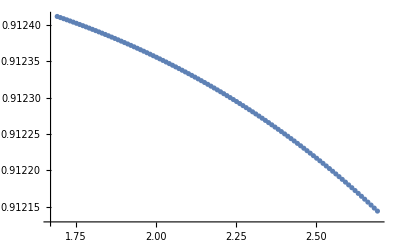

```mathematica
ListPlot[%]
```

```mathematica
FullSimplify[g[δ[x0, ϵ0]]==h[x0, ϵ0]]
```

1/(√(1-4 λ))((1-4 λ) Log[ϵ0 (-x0 √(1-4 λ)+ϵ0 λ)]+Log[(2 (1-1/(√(1-4 λ))) δ[x0,ϵ0])/(1+√(1-4 λ)+2 δ[x0,ϵ0])]-√(1-4 λ) (-2 ArcTanh[1-(2 ϵ0 λ)/(x0 √(1-4 λ))]+Log[(δ[x0,ϵ0] (√(1-4 λ)+δ[x0,ϵ0]))/(1+√(1-4 λ)+2 δ[x0,ϵ0])^2]+2 Log[1+√(1-4 λ)+2 δ[x0,ϵ0]])-Log[1+(1+√(1-4 λ)-4 λ+2 δ[x0,ϵ0])/(√(1-4 λ) (1+√(1-4 λ)+2 δ[x0,ϵ0]))])==0

```mathematica
FullSimplify[D[(ϵ0 (1+√(1-4 λ)) λ)/(x0-4 x0 λ)+(Log[ϵ0 (1+√(1-4 λ)-2 λ)]-Log[2 x0 δ[x0,ϵ0]])/(√(1-4 λ))+((1+√(1-4 λ)) δ[x0,ϵ0])/(-1+4 λ)==Log[(x0 ϵ0)/δ[x0,ϵ0]], ϵ0]]
```

1/(ϵ0 √(1-4 λ))+((1+√(1-4 λ)) λ)/(x0-4 x0 λ)+((1+√(1-4 λ))/(-1+4 λ)+(1-1/(√(1-4 λ)))/δ[x0,ϵ0]) δ^(0,1)[x0,ϵ0]==1/ϵ0

```mathematica
Solve[%, Derivative[0,1][δ][x0,ϵ0]]
```

{{δ^(0,1)[x0,ϵ0]→(1/ϵ0-1/(ϵ0 √(1-4 λ))-((1+√(1-4 λ)) λ)/(x0-4 x0 λ))/((1+√(1-4 λ))/(-1+4 λ)+(1-1/(√(1-4 λ)))/δ[x0,ϵ0])}}

```mathematica
FullSimplify[(1/ϵ0-1/(ϵ0 √(1-4 λ))-((1+√(1-4 λ)) λ)/(x0-4 x0 λ))/((1+√(1-4 λ))/(-1+4 λ)+(1-1/(√(1-4 λ)))/δ[x0,ϵ0])]
```

((ϵ0 (1+√(1-4 λ)-4 λ) λ+x0 (-1+√(1-4 λ)) (-1+4 λ)) δ[x0,ϵ0])/(x0 ϵ0 ((-1+√(1-4 λ)) (-1+4 λ)+(1+√(1-4 λ)-4 λ) δ[x0,ϵ0]))

```mathematica
Limit[%4, ϵ0->0]
```

lim_(ϵ0→0) ((ϵ0 (1+√(1-4 λ)-4 λ) λ+x0 (-1+√(1-4 λ)) (-1+4 λ)) δ[x0,ϵ0])/(x0 ϵ0 ((-1+√(1-4 λ)) (-1+4 λ)+(1+√(1-4 λ)-4 λ) δ[x0,ϵ0]))

```mathematica
D[(ϵ0 (1+√(1-4 λ)-4 λ) λ+x0 (-1+√(1-4 λ)) (-1+4 λ)) δ[x0,ϵ0], ϵ0]/D[x0 ϵ0 ((-1+√(1-4 λ)) (-1+4 λ)+(1+√(1-4 λ)-4 λ) δ[x0,ϵ0]), ϵ0]
```

((1+√(1-4 λ)-4 λ) λ δ[x0,ϵ0]+(ϵ0 (1+√(1-4 λ)-4 λ) λ+x0 (-1+√(1-4 λ)) (-1+4 λ)) δ^(0,1)[x0,ϵ0])/(x0 ((-1+√(1-4 λ)) (-1+4 λ)+(1+√(1-4 λ)-4 λ) δ[x0,ϵ0])+x0 ϵ0 (1+√(1-4 λ)-4 λ) δ^(0,1)[x0,ϵ0])

```mathematica
%/.Derivative[0,1][δ][x0,ϵ0]->((ϵ0 (1+√(1-4 λ)-4 λ) λ+x0 (-1+√(1-4 λ)) (-1+4 λ)) δ[x0,ϵ0])/(x0 ϵ0 ((-1+√(1-4 λ)) (-1+4 λ)+(1+√(1-4 λ)-4 λ) δ[x0,ϵ0]))
```

((1+√(1-4 λ)-4 λ) λ δ[x0,ϵ0]+((ϵ0 (1+√(1-4 λ)-4 λ) λ+x0 (-1+√(1-4 λ)) (-1+4 λ))^2 δ[x0,ϵ0])/(x0 ϵ0 ((-1+√(1-4 λ)) (-1+4 λ)+(1+√(1-4 λ)-4 λ) δ[x0,ϵ0])))/(((1+√(1-4 λ)-4 λ) (ϵ0 (1+√(1-4 λ)-4 λ) λ+x0 (-1+√(1-4 λ)) (-1+4 λ)) δ[x0,ϵ0])/((-1+√(1-4 λ)) (-1+4 λ)+(1+√(1-4 λ)-4 λ) δ[x0,ϵ0])+x0 ((-1+√(1-4 λ)) (-1+4 λ)+(1+√(1-4 λ)-4 λ) δ[x0,ϵ0]))

```mathematica
FullSimplify[%]
```

(δ[x0,ϵ0] (6 x0 ϵ0 √(1-4 λ) λ^2+ϵ0^2 (1+√(1-4 λ)-2 λ) λ^2+x0^2 (-1+√(1-4 λ)+2 λ) (-1+4 λ)+x0 ϵ0 (1+√(1-4 λ)-2 λ) λ δ[x0,ϵ0]))/(x0 ϵ0 (x0 (-1+√(1-4 λ)+2 λ) (-1+4 λ)+δ[x0,ϵ0] (6 x0 √(1-4 λ) λ+ϵ0 (1+√(1-4 λ)-2 λ) λ+x0 (1+√(1-4 λ)-2 λ) δ[x0,ϵ0])))

```mathematica
Limit[%, ϵ0 ->0]
```

lim_(ϵ0→0) (δ[x0,ϵ0] (6 x0 ϵ0 √(1-4 λ) λ^2+ϵ0^2 (1+√(1-4 λ)-2 λ) λ^2+x0^2 (-1+√(1-4 λ)+2 λ) (-1+4 λ)+x0 ϵ0 (1+√(1-4 λ)-2 λ) λ δ[x0,ϵ0]))/(x0 ϵ0 (x0 (-1+√(1-4 λ)+2 λ) (-1+4 λ)+δ[x0,ϵ0] (6 x0 √(1-4 λ) λ+ϵ0 (1+√(1-4 λ)-2 λ) λ+x0 (1+√(1-4 λ)-2 λ) δ[x0,ϵ0])))

```mathematica
Series[%181,{λ,0,2}]
```

((x0+ϵ0) λ)/(x0 ϵ0)+((-x0-ϵ0) λ^2)/(x0 ϵ0 δ[x0,ϵ0])+O[λ]^3

```mathematica
D[%, ϵ0]
```

-((δ^(0,1)[x0,ϵ0])^2)/δ[x0,ϵ0]^2+((1+√(1-4 λ)) δ^(0,2)[x0,ϵ0])/(-1+4 λ)+(δ^(0,2)[x0,ϵ0])/δ[x0,ϵ0]+(-1/ϵ0^2+((δ^(0,1)[x0,ϵ0])^2)/δ[x0,ϵ0]^2-(δ^(0,2)[x0,ϵ0])/δ[x0,ϵ0])/(√(1-4 λ))

```mathematica
FullSimplify[D[(ϵ0 λ)/x0+((-1+4 λ) Log[(x0 ϵ0)/δ[x0,ϵ0]])/(1+√(1-4 λ)), ϵ0]]
```

λ/x0+((-1+4 λ) (δ[x0,ϵ0]-ϵ0 δ^(0,1)[x0,ϵ0]))/(ϵ0 (1+√(1-4 λ)) δ[x0,ϵ0])

```mathematica
Solve[%==Derivative[0,1][δ][x0,ϵ0], Derivative[0,1][δ][x0,ϵ0]]
```

{{δ^(0,1)[x0,ϵ0]→((-x0+4 x0 λ+ϵ0 λ+ϵ0 √(1-4 λ) λ) δ[x0,ϵ0])/(x0 ϵ0 (-1+4 λ+δ[x0,ϵ0]+√(1-4 λ) δ[x0,ϵ0]))}}

```mathematica
FullSimplify[%]
```

{{δ^(0,1)[x0,ϵ0]→((ϵ0 (1+√(1-4 λ)) λ+x0 (-1+4 λ)) δ[x0,ϵ0])/(x0 ϵ0 (-1+4 λ+(1+√(1-4 λ)) δ[x0,ϵ0]))}}

```mathematica
Limit[((ϵ0 (1+√(1-4 λ)) λ+x0 (-1+4 λ)) δ[x0,ϵ0])/(x0 ϵ0 (-1+4 λ+(1+√(1-4 λ)) δ[x0,ϵ0])), {δ[x0,ϵ0]->(1+Sqrt[1-4λ])/2}]
```

((1+√(1-4 λ)) (ϵ0 (1+√(1-4 λ)) λ+x0 (-1+4 λ)))/(2 x0 ϵ0 (-1+1/2 (1+√(1-4 λ))^2+4 λ))

```mathematica
FullSimplify[%]
```

((1+√(1-4 λ)) (ϵ0 (1+√(1-4 λ)) λ+x0 (-1+4 λ)))/(2 x0 ϵ0 (√(1-4 λ)+2 λ))

```mathematica
Limit[(1+√(1-4 λ)) (ϵ0 (1+√(1-4 λ)) λ+x0 (-1+4 λ)), ϵ0->0]
```

x0 (1+√(1-4 λ)) (-1+4 λ)

```mathematica
Solve[%, δ[x0,ϵ0]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(ϵ0 λ)/x0+((-1+4 λ) Log[(x0 ϵ0)/δ[x0,ϵ0]])/(1+√(1-4 λ))==δ[x0,ϵ0],δ[x0,ϵ0]]

```mathematica
%774[[1, 1, 1]]
```

((ϵ0 (1+√(1-4 λ)) λ)/x0+(-1+4 λ) (2 Log[x0]+Log[-ϵ0/x0]-Log[-δ[x0,ϵ0]]))/(1+√(1-4 λ))==δ[x0,ϵ0]

```mathematica
FullSimplify[%]
```

((ϵ0 (1+√(1-4 λ)) λ)/x0+(-1+4 λ) (2 Log[x0]+Log[-ϵ0/x0]-Log[-δ[x0,ϵ0]])==(1+√(1-4 λ)) δ[x0,ϵ0])/(1+√(1-4 λ))

```mathematica
Solve[%, δ]
```

Solve[(ϵ0 (1+√(1-4 λ)) λ)/x0+(-1+4 λ) (2 Log[x0]-Log[-δ]+Log[-ϵ0/x0])==δ (1+√(1-4 λ)),δ]

```mathematica
dgdf=FullSimplify[D[g[f[x0,y0]], f[x0,y0]]]
```

(2 (-1+f[x0,y0]))/(λ+(-1+f[x0,y0]) f[x0,y0])

```mathematica
dhdx = FullSimplify[D[h[x0,y0], x0]]
```

(2 (x0-y0))/(x0^2-x0 y0+y0^2 λ)

```mathematica
dfdx =FullSimplify[ dhdx/dgdf]
```

((x0-y0) (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))

```mathematica
Limit[dfdx, {f[x0, y0]->(1+Sqrt[1-4λ])/2,y0->x0((1+Sqrt[1-4λ])/2)^-1}]
```

$Aborted

```mathematica
f[x0, y0]->(1+Sqrt[1-4λ])/2
```

```mathematica
Limit[(x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]),  f[x0, y0]->(1+Sqrt[1-4λ])/2]
```

(-1+1/2 (1+√(1-4 λ))) (x0^2-x0 y0+y0^2 λ)

```mathematica
Limit[(-1+1/2 (1+√(1-4 λ))) (x0^2-x0 y0+y0^2 λ),y0->x0((1+Sqrt[1-4λ])/2)^-1]
```

(-1+1/2 (1+√(1-4 λ))) (x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2)

```mathematica
FullSimplify[%]
```

0

```mathematica
%/.f[x0,y0]->(1+Sqrt[1-4λ])/2
```

((x0-y0) (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ))/((-1+1/2 (1+√(1-4 λ))) (x0^2-x0 y0+y0^2 λ))

```mathematica
FullSimplify[%]
```

0

```mathematica
%308/.y0->((1+Sqrt[1-4λ])/2)^-1 x0
```

((x0-(2 x0)/(1+√(1-4 λ))) (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ))/((-1+1/2 (1+√(1-4 λ))) (x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2))

```mathematica
FullSimplify[%]
```

(1+√(1-4 λ))/(2 x0)

```mathematica
dhdy=FullSimplify[D[h[x0,y0], y0]]
```

(2 y0 λ)/(x0^2-x0 y0+y0^2 λ)

```mathematica
dfdy = FullSimplify[dhdy/dgdf]
```

(y0 λ (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))

```mathematica
Limit[%675, {y0->x0((1+Sqrt[1-4λ])/2)^-1}]
```

```mathematica
%/.f[x0,y0]->(1+Sqrt[1-4λ])/2
```

(y0 λ (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ))/((-1+1/2 (1+√(1-4 λ))) (x0^2-x0 y0+y0^2 λ))

```mathematica
FullSimplify[(y0 λ (1/2 (1+√(1-4 λ))+λ))/(x0^2-x0 y0+y0^2 λ)]
```

(y0 λ (1+√(1-4 λ)+2 λ))/(2 (x0^2-x0 y0+y0^2 λ))

```mathematica
%680/.y0->x0*2/(1+Sqrt[1-4λ])
```

(x0 λ (1+√(1-4 λ)+2 λ))/((1+√(1-4 λ)) (x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2))

```mathematica
FullSimplify[(x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2)]
```

0

```mathematica
Expand[%685]
```

(x0 λ)/((1+√(1-4 λ)) (x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2))+(x0 √(1-4 λ) λ)/((1+√(1-4 λ)) (x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2))+(2 x0 λ^2)/((1+√(1-4 λ)) (x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2))

```mathematica
Factor[%676]
```

0

```mathematica
FullSimplify[%]
```

0

```mathematica
Clear[f]
```

```mathematica
D[%587, y0]
```

-(y0 λ (-x0+2 y0 λ) (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ)^2 (-1+f[x0,y0]))+(λ (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))-(y0 λ (λ+(-1+f[x0,y0]) f[x0,y0]) f^(0,1)[x0,y0])/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0])^2)+(y0 λ ((-1+f[x0,y0]) f^(0,1)[x0,y0]+f[x0,y0] f^(0,1)[x0,y0]))/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))

```mathematica
%/.Derivative[0,1][f][x0,y0]->dfdy
```

-(y0 λ (-x0+2 y0 λ) (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ)^2 (-1+f[x0,y0]))+(λ (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))-(y0^2 λ^2 (λ+(-1+f[x0,y0]) f[x0,y0])^2)/((x0^2-x0 y0+y0^2 λ)^2 (-1+f[x0,y0])^3)+(y0 λ ((y0 λ (λ+(-1+f[x0,y0]) f[x0,y0]))/(x0^2-x0 y0+y0^2 λ)+(y0 λ f[x0,y0] (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))))/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))

```mathematica
FullSimplify[%]
```

-(λ (x0+y0 λ-x0 f[x0,y0]) (-x0+y0 λ+x0 f[x0,y0]) (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ)^2 (-1+f[x0,y0])^3)

```mathematica
%625/.{λ->0.08, f[x0, y0]->(1+Sqrt[1-4*0.08])/2}
```

-(3.29305×10^-15 (-0.0876894 x0+0.08 y0) (0.0876894 x0+0.08 y0))/((x0^2-x0 y0+0.08 y0^2)^2)

```mathematica
FullSimplify[%]
```

(0.+2.53217×10^-17 x0^2-2.10755×10^-17 y0^2)/((x0^2-1. x0 y0+0.08 y0^2)^2)

```mathematica
(x0^2-1. x0 y0+0.08 y0^2)^2/.{x0->x0h, y0->y0h}
```

2.77334×10^-32

```mathematica
%587/.{λ->0.08, f[x0, y0]->1/slope[0.08], y0->y0h, x0->x0h}
```

-0.666667

```mathematica
%/.y0->((1+Sqrt[1-4λ])/2)^-1 x0
```

(2 x0 λ (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ))/((-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ)) (x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2))

```mathematica
FullSimplify[%]
```

-(1+√(1-4 λ)-2 λ)/(2 x0)

```mathematica
d2fdx2=D[dfdx,x0]
```

-((x0-y0) (2 x0-y0) (λ+(-1+f[x0,y0]) f[x0,y0]))/((x0^2-x0 y0+y0^2 λ)^2 (-1+f[x0,y0]))+(λ+(-1+f[x0,y0]) f[x0,y0])/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))-((x0-y0) (λ+(-1+f[x0,y0]) f[x0,y0]) f^(1,0)[x0,y0])/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0])^2)+((x0-y0) ((-1+f[x0,y0]) f^(1,0)[x0,y0]+f[x0,y0] f^(1,0)[x0,y0]))/((x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]))

```mathematica
%/.f[x0,y0]->(1+Sqrt[1-4λ])/2
```

-((x0-y0) (2 x0-y0) (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ))/((-1+1/2 (1+√(1-4 λ))) (x0^2-x0 y0+y0^2 λ)^2)+(1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ)/((-1+1/2 (1+√(1-4 λ))) (x0^2-x0 y0+y0^2 λ))-((x0-y0) (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ) f^(1,0)[x0,y0])/((-1+1/2 (1+√(1-4 λ)))^2 (x0^2-x0 y0+y0^2 λ))+((x0-y0) ((-1+1/2 (1+√(1-4 λ))) f^(1,0)[x0,y0]+1/2 (1+√(1-4 λ)) f^(1,0)[x0,y0]))/((-1+1/2 (1+√(1-4 λ))) (x0^2-x0 y0+y0^2 λ))

```mathematica
FullSimplify[d2fdx2/.Derivative[1,0][f][x0,y0]->(1+√(1-4 λ))/(2 x0)]
```

((x0-y0) (1+√(1-4 λ)) (x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]) (-1+2 f[x0,y0])-(x0-y0) (1+√(1-4 λ)) (x0^2-x0 y0+y0^2 λ) (λ+(-1+f[x0,y0]) f[x0,y0])-2 x0 (x0-y0) (2 x0-y0) (-1+f[x0,y0]) (λ+(-1+f[x0,y0]) f[x0,y0])+2 x0 (x0^2-x0 y0+y0^2 λ) (-1+f[x0,y0]) (λ+(-1+f[x0,y0]) f[x0,y0]))/(2 x0 (x0^2-x0 y0+y0^2 λ)^2 (-1+f[x0,y0])^2)

```mathematica
%/.f[x0,y0]->(1+Sqrt[1-4λ])/2
```

(-2 x0 (x0-y0) (2 x0-y0) (-1+1/2 (1+√(1-4 λ))) (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ)+(x0-y0) (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ)) √(1-4 λ) (x0^2-x0 y0+y0^2 λ)+2 x0 (-1+1/2 (1+√(1-4 λ))) (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ) (x0^2-x0 y0+y0^2 λ)-(x0-y0) (1+√(1-4 λ)) (1/2 (-1+1/2 (1+√(1-4 λ))) (1+√(1-4 λ))+λ) (x0^2-x0 y0+y0^2 λ))/(2 x0 (-1+1/2 (1+√(1-4 λ)))^2 (x0^2-x0 y0+y0^2 λ)^2)

```mathematica
FullSimplify[%]
```

(4 (-x0+y0) √(1-4 λ) λ)/(x0 (-1+√(1-4 λ))^2 (x0^2-x0 y0+y0^2 λ))

```mathematica
%/.y0->((1+Sqrt[1-4λ])/2)^-1 x0
```

(4 (-x0+(2 x0)/(1+√(1-4 λ))) √(1-4 λ) λ)/(x0 (-1+√(1-4 λ))^2 (x0^2-(2 x0^2)/(1+√(1-4 λ))+(4 x0^2 λ)/(1+√(1-4 λ))^2))

```mathematica
Factor[(x0^2-x0 y0+y0^2 λ)]
```

x0^2-x0 y0+y0^2 λ

```mathematica
(x0^2-x0 y0+y0^2 λ)/(-x0+y0)
```

(x0^2-x0 y0+y0^2 λ)/(-x0+y0)

```mathematica
FullSimplify[((-x0+y0)/(x0 (x0^2-x0 y0+y0^2 λ)))^-1]
```

x0 (-x0-(y0^2 λ)/(x0-y0))

```mathematica
%^-1
```

1/(x0 (-x0-(y0^2 λ)/(x0-y0)))

```mathematica
%/.y0->((1+Sqrt[1-4λ])/2)^-1 x0
```

1/(x0 (-x0-(4 x0^2 λ)/((x0-(2 x0)/(1+√(1-4 λ))) (1+√(1-4 λ))^2)))

```mathematica
FullSimplify[-x0-(4 x0^2 λ)/((x0-(2 x0)/(1+√(1-4 λ))) (1+√(1-4 λ))^2)]
```

0

```mathematica
(2 ArcTan[(-1+(2 λ)/x)/(√(-1+4 λ))])/(√(-1+4 λ))+2 Log[x]+Log[(-x+x^2+λ)/x^2]-((2 ArcTan[(-1+(2 y0 λ)/x0)/(√(-1+4 λ))])/(√(-1+4 λ))+2 Log[x0]+Log[(x0^2-x0 y0+y0^2 λ)/x0^2])
```

(2 ArcTan[(-1+(2 λ)/x)/(√(-1+4 λ))])/(√(-1+4 λ))-(2 ArcTan[(-1+(2 y0 λ)/x0)/(√(-1+4 λ))])/(√(-1+4 λ))+2 Log[x]-2 Log[x0]+Log[(-x+x^2+λ)/x^2]-Log[(x0^2-x0 y0+y0^2 λ)/x0^2]

```mathematica
FullSimplify[%]
```

(2 (ArcTan[(-1+(2 λ)/x)/(√(-1+4 λ))]-ArcTan[(-1+(2 y0 λ)/x0)/(√(-1+4 λ))]))/(√(-1+4 λ))+2 Log[x]-2 Log[x0]+Log[((-1+x) x+λ)/x^2]-Log[(x0^2-x0 y0+y0^2 λ)/x0^2]

```mathematica
Re[(2 (ArcTan[(-1+(2 λ)/x)/(√(-1+4 λ))]-ArcTan[(-1+(2 y0 λ)/x0)/(√(-1+4 λ))]))/(√(-1+4 λ))]+Re[2 Log[x]]-Re[2 Log[x0]]+Re[Log[((-1+x) x+λ)/x^2]]-Re[Log[(x0^2-x0 y0+y0^2 λ)/x0^2]]
```

2 Re[(ArcTan[(-1+(2 λ)/x)/(√(-1+4 λ))]-ArcTan[(-1+(2 y0 λ)/x0)/(√(-1+4 λ))])/(√(-1+4 λ))]+2 Re[Log[x]]-2 Re[Log[x0]]+Re[Log[((-1+x) x+λ)/x^2]]-Re[Log[(x0^2-x0 y0+y0^2 λ)/x0^2]]

```mathematica
{xh, 4, 6, 0.5}
```

{xh,4,6,0.5}

```mathematica
Table[FindRoot[%138/.{λ->0.1, y0->2, x0->xh}, {x, 0.97}, MaxIterations->1000, AccuracyGoal->16],{xh, 1.5, 2.5, 0.005}]
```

{{x→0.882135},{x→0.892775},{x→0.892496},{x→0.892231},{x→0.891979},{x→0.891739},{x→0.891511},{x→0.891294},{x→0.891087},{x→0.89089},{x→0.884115},{x→0.884272},{x→0.884423},{x→0.884567},{x→0.884706},{x→0.889888},{x→0.889747},{x→0.885088},{x→0.889484},{x→0.889362},{x→0.889246},{x→0.889135},{x→0.889029},{x→0.885721},{x→0.888831},{x→0.888739},{x→0.888651},{x→0.888567},{x→0.888487},{x→0.888411},{x→0.888338},{x→0.886347},{x→0.886411},{x→0.886472},{x→0.886531},{x→0.88802},{x→0.88664},{x→0.887913},{x→0.88674},{x→0.887815},{x→0.88777},{x→0.886874},{x→0.887685},{x→0.887646},{x→0.88699},{x→0.887572},{x→0.887538},{x→0.887506},{x→0.887475},{x→0.887152},{x→0.887417},{x→0.887206},{x→-3.00737},{x→-3.21015},{x→-3.589},{x→-5.14084},{x→-3.53121},{x→-3.22},{x→-3.0512},{x→0.887377},{x→0.887394},{x→0.887187},{x→0.887172},{x→0.887158},{x→0.887453},{x→0.887466},{x→0.887478},{x→0.887489},{x→0.8875},{x→0.88751},{x→0.88752},{x→0.887529},{x→0.887538},{x→0.887546},{x→0.887553},{x→0.88756},{x→0.887031},{x→0.887573},{x→0.887579},{x→0.887014},{x→0.887009},{x→0.887005},{x→0.887001},{x→0.886997},{x→0.886993},{x→0.88699},{x→0.887612},{x→0.886984},{x→0.887617},{x→0.887619},{x→0.887621},{x→0.887623},{x→0.886975},{x→0.886973},{x→0.887627},{x→0.887627},{x→0.887628},{x→0.887629},{x→0.887629},{x→0.887629},{x→0.887629},{x→0.887629},{x→0.887629},{x→0.887629},{x→0.887628},{x→0.887628},{x→0.887627},{x→0.887626},{x→0.886973},{x→0.886974},{x→0.887623},{x→0.887622},{x→0.887621},{x→0.88762},{x→0.887618},{x→0.887617},{x→0.887615},{x→0.886985},{x→0.887612},{x→0.88761},{x→0.88699},{x→0.886992},{x→0.886993},{x→0.886995},{x→0.886997},{x→0.886999},{x→0.887001},{x→0.887003},{x→0.887005},{x→0.887007},{x→0.887009},{x→0.887011},{x→0.887013},{x→0.887015},{x→0.887581},{x→0.887579},{x→0.887577},{x→0.887574},{x→0.887572},{x→0.887028},{x→0.88703},{x→0.887033},{x→0.887563},{x→0.887037},{x→0.887559},{x→0.887557},{x→0.887554},{x→0.887552},{x→0.88755},{x→0.887548},{x→0.887546},{x→0.887543},{x→0.887541},{x→0.887539},{x→0.887537},{x→0.887535},{x→0.887532},{x→0.88753},{x→0.887528},{x→0.887526},{x→0.887524},{x→0.887522},{x→0.887519},{x→0.887517},{x→0.887515},{x→0.887513},{x→0.887511},{x→0.887509},{x→0.887507},{x→0.887505},{x→0.887503},{x→0.887501},{x→0.887499},{x→0.887497},{x→0.887495},{x→0.887493},{x→0.887491},{x→0.887489},{x→0.887487},{x→0.887485},{x→0.887483},{x→0.887482},{x→0.88748},{x→0.887478},{x→0.887476},{x→0.887474},{x→0.887472},{x→0.887471},{x→0.887469},{x→0.887467},{x→0.887465},{x→0.887464},{x→0.887462},{x→0.88746},{x→0.887459},{x→0.887457},{x→0.887142},{x→0.887454},{x→0.887452},{x→0.887451},{x→0.887148}}

```mathematica
x/.%;
```

```mathematica
Table[xh,  {xh, 1.5, 2.5, 0.005}];
```

```mathematica
Transpose[Join[{%229, %228}]];
```

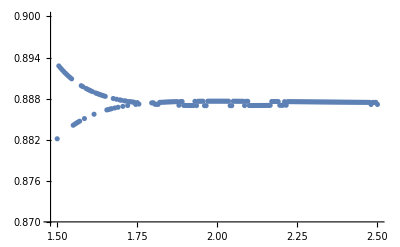

```mathematica
ListPlot[%223, PlotRange->{0.87,0.9}]
```

```mathematica
Solve[1==(2/(1+Sqrt[1-4*0.02]))x, x]
```

{{x→0.979583}}

```mathematica
ArcTanh[1.99999]
```

0.549309-1.5708 ⅈ

```mathematica
ArcTan[x]/ArcTanh[x]
```

ArcTan[x]/ArcTanh[x]

```mathematica
FullSimplify[%]
```

ArcTan[x]/ArcTanh[x]

```mathematica
Table[NSolve[%11,x],{x0,1,10,0.2}]
```

{NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==1.80213+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.00019+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.16525+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.30684+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.43089+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.54133+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.64094+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.73171+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.81516+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.89247+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==2.96457+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.03222+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.09606+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.15666+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.21454+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.27025+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.32441+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.37798+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.43302+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.49836+1.50665 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.53834-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.5554-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.58272-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.61218-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.64206-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.67177-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.70103-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.72972-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.7578-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.78522-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.812-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.83815-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.86367-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.88858-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.91291-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.93668-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.9599-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==3.9826-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==4.00479-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==4.02651-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==4.04775-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==4.06856-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==4.08893-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==4.10889-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==4.12845-1.5708 ⅈ,x],NSolve[1. ArcTanh[1.04257-0.0417029/x]+0.959166 Log[x]+0.479583 Log[(0.02+(-1.+x) x)/x^2]==4.14763-1.5708 ⅈ,x]}